## DEFINE PARAMETERS

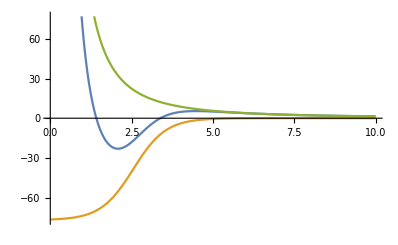

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=77;R=2.55;a=0.5;μ=8/9 Subscript[m, N];l=2;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

```mathematica
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0:=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
```

## BOUND SOLUTIONS

```mathematica
(*BOUND SOLUTION*)
κ[En_]:=Sqrt[(2μ Abs[En])/ℏc^2];
wavebound[En_,r_,l_]:=SphericalHankelH1[l,I κ[En] r];
Bbound[En_,l_]:=rmax/wavebound[En,rmax,l](D[wavebound[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_,l_}]:=({evalbound,evecbound}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En,l]]],First];{evalbound[[i]],i,l})
```

```mathematica
ϵ=10^-10;
n=1;
evalsbound=List[];evecsbound=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evalsbound=Append[evalsbound,En];
evecsbound=Append[evecsbound,evecbound[[n]]];n++;En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];]
```

```mathematica
evalsbound
```

{}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound[i_]:=evecsbound[[i,-1]]/Abs[wavebound[evalsbound[[i]],rmax,l]];
rmaxx=25.;
normbound[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[evecsbound⟦i⟧,constbound[i] wavebound[evalsbound[[i]],Range[rmax+dr,rmaxx,dr],l]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
Manipulate[ListLinePlot[{Transpose[{rlist,normbound[i] evecsbound⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],normbound[i]constbound[i]Abs[wavebound[evalsbound[[i]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All],{i,1,Length[evalsbound],1}]
```

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
waveres[En_?NumericQ,r_,l_]:=SphericalHankelH1[l,k[En] r];
Bres[En_?NumericQ,l_]:=rmax/waveres[En,rmax,l](D[waveres[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_,l_}]:=({evalres,evecres}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];{evalres[[i]],i,l})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=1;
evalsres=List[];evecsres=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];evecsres=Append[evecsres,evecres[[n]]];
```

```mathematica
evalsres
```

{0.17644-0.000358926 ⅈ}

```mathematica
For[i=2,i≤5,i++,En=NestWhileList[eigenvres,{0,i,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];
evecsres=Append[evecsres,evecres[[i]]];]
```

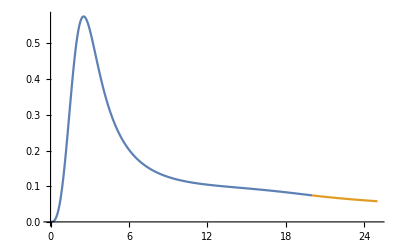

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres[i_]:=evecsres[[i,-1]]/waveres[evalsres[[i]],rmax,l];
rmaxx=25.;
normres[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[evecsres⟦i⟧,constres[i] waveres[evalsres[[i]],Range[rmax+dr,rmaxx,dr],l]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
ListLinePlot[{Transpose[{rlist,normres[1] Abs[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],normres[1]Abs[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All]
```

```mathematica
evalsres
```

{0.17644-0.000358926 ⅈ}

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
ks[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
wavescat1[En_,r_,δ_,l_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[l,ks[En] r]-Sin[δ] SphericalBesselY[l,ks[En] r]);
wavescat[En_,r_,δ_,l_]:=(Cos[δ]SphericalBesselJ[l,ks[En] r]+Sin[δ] SphericalBesselY[l,ks[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat[En_?NumericQ,δ_?NumericQ,l_]:=rmax/wavescat[En,rmax,δ,l] D[wavescat[En,r,δ,l],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat[En,δ,l]/rmax-1);H);
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ,l_]:=({evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];evalscat[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x,l],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x,l]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE AND PLOTS*)
constscat[i_]:=evecscat[[i,-1]]/wavescat[evalscat[[i]],rmax,δ,l];
rmaxx=25.;
normscat[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[evecscat⟦i⟧,constscat[i] wavescat[evalscat[[i]],Range[rmax+dr,rmaxx,dr],δ,l]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];Print[{En,evalscat[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,normscat[n] Abs[evecscat⟦n⟧]}],Transpose[{Range[rmax,rmaxx,dr],normscat[n] Abs[constscat[n] wavescat[evalscat[[n]],Range[rmax,rmaxx,dr],δ,l]]}]},PlotRange->All]]
```

{0.17644,0.17644,1,1.57739}

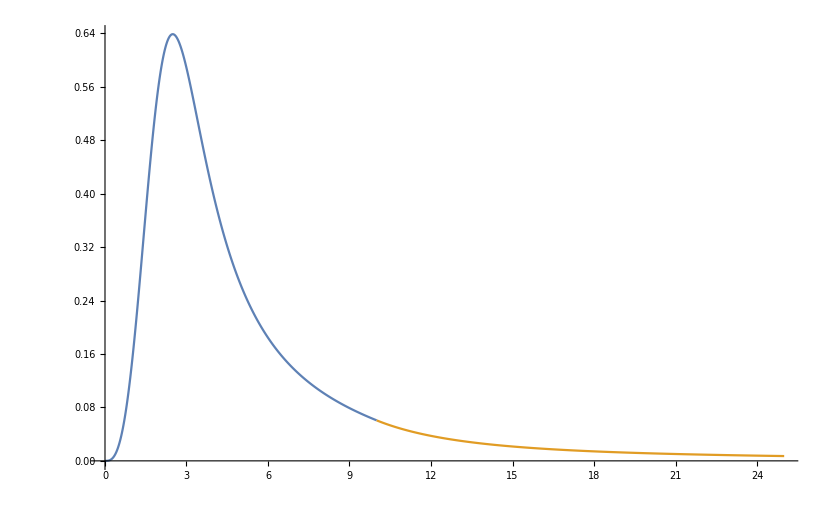
{67.328,-Graphics-}

```mathematica
wvplot[0.1764403397030842]//Timing
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.17,0.18,0.001}];
```

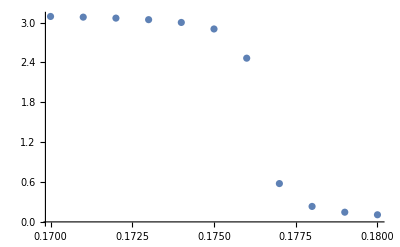

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

```mathematica
findres[n_]:=(phase[y_?NumericQ]:=Re[FindRoot[eigenvscat[y,n,x,l]==y,{x,0.,-Pi,Pi}][[1,2]]];Subscript[δ, res]=y/.FindRoot[phase[y]==Pi/2,{y,0.1765,0.1760,0.1770}])
```

```mathematica
Subscript[δ, res]=findres[1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.176} is at the edge of the search region {0.176,0.177} in coordinate 1 and the computed search direction points outside the region.

0.176

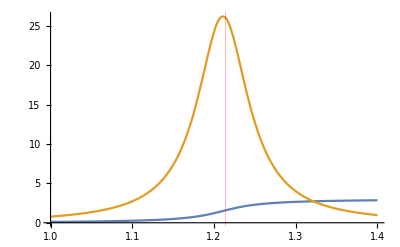

```mathematica
funcphasedata=Interpolation[phasedata,Method->"Spline"];
dfuncphasedata=funcphasedata';
Plot[Evaluate[{funcphasedata[x],dfuncphasedata[x]}],{x,1.0,1.4},PlotRange->All,GridLines->{{{Subscript[δ, res],Red}},None}]
```

```mathematica
1/(D[funcphasedata[x],x]/.x->findres[1])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0383736